```mathematica
SetOptions[$FrontEnd,"CommonDefaultFormatTypes"->{"Output"->StandardForm}]
basepath=$HomeDirectory<>"/sivers_TMD_PhD_project/mathematica_hari"
SetDirectory[basepath<>"/output"];
includepath=basepath<>"/include";
AppendTo[$Path, includepath];
Needs["LatticeAnalysis`"];
 <<"LatticeAnalysis`"
(* do not keep track of intermediate results *)
$HistoryLength=0;
Needs["FourierSeries`"]
lata=0.11403
```

/Users/hariprashadravikumar/sivers_TMD_PhD_project/mathematica_hari

0.11403

## Open Database

```mathematica
AmpDB = BIDATEXReader["/Users/hariprashadravikumar/sivers_TMD_PhD_project/sivers_new/newDBforA12BA2B/db_Alleta_correct_try_A12B_A2B_bL_bT_bevenodd.bidatex"]
AmpDBPbbsq = BIDATEXReader["/Users/hariprashadravikumar/sivers_TMD_PhD_project/sivers_new/newDBforA12BA2B/db_Alleta_correct_try_A12B_A2B_Pb32by2Pi_bsq_bevenodd.bidatex"]
```

< -MemDB- {A,bL,bNum,bT,data,EN,etav,MN,PL,zta}>

< -MemDB- {A,bNum,bsquare,data,EN,etav,MN,Pb32by2Pi,PL,zta}>

```mathematica
MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->A12B}],{PL,zta}]//Union
```

{{-4,⟨0.786(34)⟩_(RowBox[{)},{-3,⟨0.540(12)⟩_(RowBox[{)},{-2,⟨0.2944(36)⟩_(RowBox[{)},{-1,⟨0.09077(75)⟩_(RowBox[{)}}

```mathematica
modelfitJackkife[model_, fitParams_, x_, y_]:=Module[{numFs, modelvaluej,modelvalue, jackknifeResults},
numFs=Length[fitParams[[1]]];
modelvaluej[j_]:=Module[{datafitParams},
datafitParams={fitParams[[1]][[j]],fitParams[[2]][[j]],fitParams[[3]][[j]]};
model[x,y,datafitParams]
];
modelvalue=Table[modelvaluej[j],{j,numFs}];
jackknifeResults=JacknifeSamples@@(modelvalue);
jackknifeResults
];
modelfitJackkifefor4D[model_,fitParams_,x_,y_,z_]:=Module[{numFs,modelvaluej,modelvalue,jackknifeResults, numParams},numFs=Length[fitParams[[1]]];
numParams=Length[fitParams];
modelvaluej[j_]:=Module[{datafitParams},datafitParams=Table[fitParams[[k,j]],{k,numParams}];
model[x,y,z,datafitParams]];
modelvalue=Table[modelvaluej[j],{j,numFs}];
jackknifeResults=JacknifeSamples@@modelvalue;
jackknifeResults];
meanfromJK[JKvalue_]:=Module[{meanvalue},
meanvalue = MakeErrBars[{{1,JKvalue}}][[1]][[1]][[2]];
meanvalue
];
errorfromJK[JKvalue_]:=Module[{errorvalue},
errorvalue = MakeErrBars[{{1,JKvalue}}][[1]][[2]][[1]][[2]];
errorvalue
];
chisqOEsigmasq[O_, E_]:=Module[{OEsigmasq, Omean,Emean, Esigmasq, Osigmasq, sigmasqTotal},
Omean=meanfromJK[O];
Emean=meanfromJK[E];
Esigmasq = (MakeErrBars[{{1,E}}][[1]][[2]][[1]][[2]])^2;
Osigmasq = (MakeErrBars[{{1,O}}][[1]][[2]][[1]][[2]])^2;
sigmasqTotal = Esigmasq+Osigmasq;
OEsigmasq = If[sigmasqTotal==0,0,((Omean-Emean)^2)/sigmasqTotal];
OEsigmasq
];

JackknifeFit3D[xyJKf_,model_,para_,vari_, modelFnName_]:=Module[
{numFs,fitParamsForFj,fitParamsList,paramLists,jackknifeResults,DoF, chisquare, observed, expected, chisquareperDoF},
numFs=Length[xyJKf[[1,3]]];
WeightList = {};
Do[
ε=10^-6;
σ=(MakeErrBars[{{1,xyJKf[[ii]][[3]]}}][[1]][[2]][[1]][[2]]);
AppendTo[WeightList,1/Max[σ,ε]^2], {ii, Length[xyJKf]}];
(*Function to extract j-th f values and fit them*)
fitParamsForFj[j_]:=Module[{data,fit},
data={#[[1]],#[[2]],#[[3,j]]}&/@xyJKf;(*Extract f_j values*)
fit=NonlinearModelFit[data,model,para,vari, Weights->WeightList,Method->{"LevenbergMarquardt"}];
fit["BestFitParameters"] (*Extract fitted parameters*)
];
(*Compute fit parameters for each f_j*)
fitParamsList=Table[fitParamsForFj[j],{j,numFs}];
jackknifeResults=Table[JacknifeSamples@@(para[[pa]]/. fitParamsList),{pa,Length[para]}];
DoF=Length[xyJKf];
chisquare=0;
Do[
observed = modelfitJackkife[modelFnName, jackknifeResults, xyJKf[[i]][[1]], xyJKf[[i]][[2]]];
expected= xyJKf[[i]][[3]];
chisquare = chisquare + chisqOEsigmasq[observed, expected];
,{i,DoF}];
chisquareperDoF=chisquare/(DoF-3);
{FitParameters->jackknifeResults, chisquareDoF->chisquareperDoF}];

JackknifeFit4D[nxyJKf_,model_,para_,vari_,modelFnName_,init_:Automatic]:=Module[{numFs,fitParamsForFj,fitParamsList,jackknifeResults,DoF,chisquare,observed,expected,chisquareperDoF},numFs=Length[nxyJKf[[1,4]]];
WeightList=Table[With[{σ=MakeErrBars[{{1,nxyJKf[[ii,4]]}}][[1,2,1,2]]},1/Max[σ,10^-6]^2],{ii,Length[nxyJKf]}];
fitParamsForFj[j_]:=Module[{data,fit},data={#[[1]],#[[2]],#[[3]],#[[4,j]]}&/@nxyJKf;
fit=NonlinearModelFit[data,model,If[init===Automatic,para,init],vari, Weights->WeightList,Method->{"LevenbergMarquardt"}];
fit["BestFitParameters"]];
fitParamsList=Table[fitParamsForFj[j],{j,numFs}];
jackknifeResults=Table[JacknifeSamples@@(para[[pa]]/. fitParamsList),{pa,Length[para]}];
jackknifeResults = jackknifeResults[[All,All, 1]];
DoF=Length[nxyJKf];
chisquare=Total[Table[observed=modelfitJackkifefor4D[modelFnName,jackknifeResults,nxyJKf[[i,1]],nxyJKf[[i,2]],nxyJKf[[i,3]]];
expected=nxyJKf[[i,4]];
chisqOEsigmasq[observed,expected],{i,DoF}]];
chisquareperDoF=chisquare/(DoF-Length[para]);
{FitParameters->jackknifeResults,chisquareDoF->chisquareperDoF}];

JackknifeFit4DGaussianCons[nxyJKf_,model_,para_,vari_,modelFnName_,init_:Automatic]:=Module[{numFs,fitParamsForFj,fitParamsList,jackknifeResults,DoF,chisquare,observed,expected,chisquareperDoF},numFs=Length[nxyJKf[[1,4]]];
WeightList=Table[With[{σ=MakeErrBars[{{1,nxyJKf[[ii,4]]}}][[1,2,1,2]]},1/Max[σ,10^-6]^2],{ii,Length[nxyJKf]}];
fitParamsForFj[j_]:=Module[{data,fit},data={#[[1]],#[[2]],#[[3]],#[[4,j]]}&/@nxyJKf;
fit=NonlinearModelFit[data,{model, c>d},If[init===Automatic,para,init],vari,Weights->WeightList];
fit["BestFitParameters"]];
fitParamsList=Table[fitParamsForFj[j],{j,numFs}];
jackknifeResults=Table[JacknifeSamples@@(para[[pa]]/. fitParamsList),{pa,Length[para]}];
jackknifeResults = jackknifeResults[[All,All, 1]];
DoF=Length[nxyJKf];
chisquare=Total[Table[observed=modelfitJackkifefor4D[modelFnName,jackknifeResults,nxyJKf[[i,1]],nxyJKf[[i,2]],nxyJKf[[i,3]]];
expected=nxyJKf[[i,4]];
chisqOEsigmasq[observed,expected],{i,DoF}]];
chisquareperDoF=chisquare/(DoF-Length[para]);
{FitParameters->jackknifeResults,chisquareDoF->chisquareperDoF}];

modelfitJackkifband[model_, fitParams_,fixedVare_, x_]:=Module[{numFs, modelvaluej,modelvalue, jackknifeResults},
numFs=Length[fitParams[[1]]];
modelvaluej[j_]:=Module[{datafitParams},
datafitParams={fitParams[[1]][[j]],fitParams[[2]][[j]],fitParams[[3]][[j]]};
model[x, fixedVare,datafitParams]
];
modelvalue=Table[modelvaluej[j],{j,numFs}];
jackknifeResults=JacknifeSamples@@(modelvalue);
jackknifeResults
];


modelfitJackkifex[model_, fitParams_, x_]:=Module[{numFs, modelvaluej,modelvalue, jackknifeResults},
numFs=Length[fitParams[[1]]];
modelvaluej[j_]:=Module[{datafitParams},
datafitParams={fitParams[[1]][[j]],fitParams[[2]][[j]],fitParams[[3]][[j]]};
model[x,datafitParams]
];
modelvalue=Table[modelvaluej[j],{j,numFs}];
jackknifeResults=JacknifeSamples@@(modelvalue);
jackknifeResults
];
modelfitJackkifex[model_, fitParams_, x_]:=Module[{numFs, modelvaluej,modelvalue, jackknifeResults},
numFs=Length[fitParams[[1]]];
modelvaluej[j_]:=Module[{datafitParams},
datafitParams={fitParams[[1]][[j]],fitParams[[2]][[j]],fitParams[[3]][[j]]};
model[x,datafitParams]
];
modelvalue=Table[modelvaluej[j],{j,numFs}];
jackknifeResults=JacknifeSamples@@(modelvalue);
jackknifeResults
];
```

## Test

```mathematica
dataforfit = MemDBGet[AmpDBPbbsq,MemDBSelect[AmpDBPbbsq,{A->A2B,PL->-2, bNum->odd}],{etav, Pb32by2Pi, bsquare,data}];
dataforfit=Select[dataforfit,#[[1]]>=6& ];
dataforfit=Select[dataforfit,#[[3]]>=9& ];
modelfitImA2B[x1_,x2_, x3_,{a_,c_, d_}]:=a*Exp[-0.5*x1]*x2*Sech[c*x2]*Sech[d*x3];
fittJKImA2B =JackknifeFit4D[dataforfit,modelfitImA2B[n, bL,bT,{a,c, d}],{{a, 0.29591435},{c,0.045}, {d,0.04}},{n,bL,bT}, modelfitImA2B]
```

{FitParameters→{⟨-0.0398(39)⟩_(RowBox[{),⟨-6.053(99) × 10⟩_(RowBox[{),⟨0.0487(29)⟩_(RowBox[{)},chisquareDoF→0.949369}

```mathematica
expr=Pb*Sech[b*Pb];
ft=FourierTransform[expr,Pb,x]//Simplify
```

(ⅈ √2 π^(3/2) Csch[(π x)/b]^2 Sinh[(π x)/(2 b)]^3)/b^2

```mathematica
expr=Pb*Sech[-b*Pb];
ft=FourierTransform[expr,Pb,x]//Simplify
```

(I*Sqrt[2]*Pi^(3/2)*Csch[(Pi*x)/b]^2*Sinh[(Pi*x)/(2*b)]^3)/b^2

```mathematica
(ⅈ √2 π^(3/2) Csch[(π x)/b]^2 Sinh[(π x)/(2 b)]^3)/b^2
```

```mathematica
modelfitA2B[x1_,x2_, x3_,{a_,c_, d_}]:=a*Exp[-0.5*x1]*Exp[-c*x2^2]*Exp[-d*x3^2];
fitJK =JackknifeFit4D[dataforfit,modelfitA2B[n, bL,bT,{a,c, d}],{{a, 2.5142937},{c,0.0764680832096769}, {d,0.0752675690340487}},{n,bL,bT}, modelfitA2B];
(*modelfitA2B[x1_,x2_, x3_,{a_, b_,c_}]:=(a*Exp[-b*x2^2]*Exp[-c*x3^2])^x1;
fitJK =JackknifeFit4D[dataforfit,modelfitA2B[n, bL,bT,{a, b,c}],{{a, 0.65},{b, 0.012},{c,0.010}},{n,bL,bT}, modelfitA2B];*)
Print[fitJK //OutputForm]
```

$Aborted

fitJK

```mathematica
fitparavalues =FitParameters/. fitJK;
Print[fitparavalues[[2]]-(fitparavalues[[3]])//OutputForm]
```

⟨0.0013(41)⟩_(2902J)

```mathematica
BB =fitparavalues[[2]]-(fitparavalues[[3]]);
```

```mathematica
InputForm[BB]
```

```mathematica
dataforfit12 = MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->A12B,PL->-2, bNum->even}],{etav, bL, bT,data}];
dataforfit12=Select[dataforfit12,#[[1]]>=6& ];
dataforfit12=Select[dataforfit12,(#[[2]]^2+#[[3]]^2)>=9& ];
modelfitA12B[x1_,x2_, x3_,{a_, b_,c_, d_}]:=a*Exp[-b*x1]*Exp[-c*x2^2]*Exp[-d*x3^2];
fitJK12 =JackknifeFit4D[dataforfit12,modelfitA12B[n, bL,bT,{a, b,c, d}],{{a, -8.15},{b, 0.57065237},{c,0.08}, {d,0.06}},{n,bL,bT}, modelfitA12B];
Print[fitJK12 //OutputForm]
```

{FitParameters -> {⟨-0.39(19)⟩_(2902J), ⟨0.530(67)⟩_(2902J), ⟨0.084(17)⟩_(2902J), ⟨0.0633(91)⟩_(2902J)}, chisquareDoF -> 0.992336}

```mathematica
fitparavalues12 =FitParameters/. fitJK12;
Print[fitparavalues12[[3]]-(fitparavalues12[[4]])//OutputForm]
```

⟨0.021(18)⟩_(2902J)

```mathematica
Print[fitparavalues12[[2]]//OutputForm]
Print[fitparavalues[[2]]//OutputForm]
Print[(fitparavalues12[[2]]-fitparavalues[[2]])//OutputForm]
```

⟨0.530(67)⟩_(2902J)

⟨0.571(18)⟩_(2902J)

⟨-0.041(69)⟩_(2902J)

```mathematica
AAA =fitparavalues12[[3]]-(fitparavalues12[[4]]);
```

⟨0.0013(41)⟩_(2902J)

0.00121951

0.00121894

0.000221442

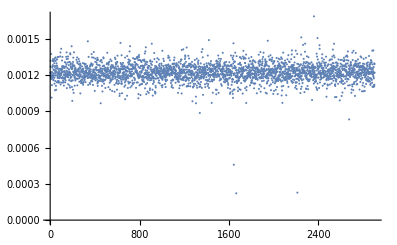

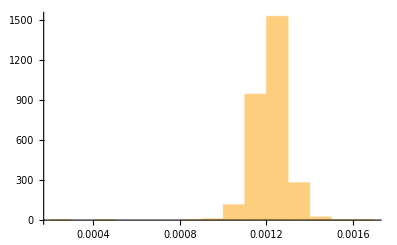

```mathematica
AAA1 = BB/. JacknifeSamples[x__]:>{x};
Print[BB//OutputForm]
AAA1//Mean
AAA1//Median
Min[AAA1]
ListPlot[AAA1, PlotRange->{0, All}]
Histogram[AAA1]
```

```mathematica
dataforfitIm2B = MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->A2B,PL->-2, bNum->odd}],{etav, bL, bT,data}];
dataforfitIm2B=Select[dataforfitIm2B,#[[1]]>=6& ];
dataforfitIm2B=Select[dataforfitIm2B,(#[[2]]^2+#[[3]]^2)>=9& ];
modelfitAIm2B[x1_,x2_, x3_,{a_,c_, d_}]:=a*Exp[-0.5*x1]*x2*Exp[-c*x2^2]*Exp[-d*x3^2];
fitJKIm2B =JackknifeFit4D[dataforfitIm2B,modelfitAIm2B[n, bL,bT,{a,c, d}],{{a, 0.29591435},{c,0.045}, {d,0.04}},{n,bL,bT}, modelfitAIm2B];
Print[fitJKIm2B //OutputForm]
```

{FitParameters -> {⟨0.129(14)⟩_(2902J), ⟨0.0429(34)⟩_(2902J), ⟨0.0483(63)⟩_(2902J)}, chisquareDoF -> 0.968257}

```mathematica
fitparavalues2BIM =FitParameters/. fitJKIm2B;
alphaminusbeta = fitparavalues2BIM[[2]]-(fitparavalues2BIM[[3]])
```

⟨-0.0054(71)⟩_(RowBox[{)

BB

-0.0055381

-0.00553391

-0.007129

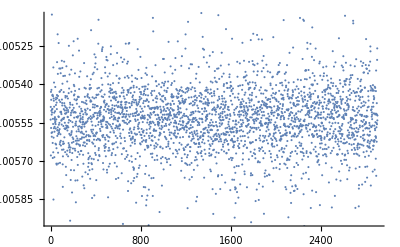

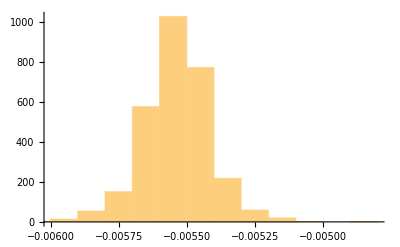

```mathematica
AAA1 = alphaminusbeta/. JacknifeSamples[x__]:>{x};
Print[BB//OutputForm]
AAA1//Mean
AAA1//Median
Min[AAA1]
ListPlot[AAA1]
Histogram[AAA1]
```

```mathematica
dataforfitIm2B = MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->A2B,PL->-2, bNum->odd}],{etav, bL, bT,data}];
dataforfitIm2B=Select[dataforfitIm2B,#[[1]]>=6& ];
dataforfitIm2B=Select[dataforfitIm2B,(#[[2]]^2+#[[3]]^2)>=9& ];
modelfitAIm2B[x1_,x2_, x3_,{a_,c_, d_}]:=a*Exp[-0.5*x1]*x2*Exp[-c*x2^2]*Exp[-d*x3^2];
fitJKIm2B =JackknifeFit4D[dataforfitIm2B,modelfitAIm2B[n, bL,bT,{a,c, d}],{{a, 0.29591435},{c,0.045}, {d,0.04}},{n,bL,bT}, modelfitAIm2B];
Print[fitJKIm2B //OutputForm]
```

{FitParameters -> {⟨0.129(14)⟩_(2902J), ⟨0.0429(34)⟩_(2902J), ⟨0.0483(63)⟩_(2902J)}, chisquareDoF -> 0.968257}

```mathematica
MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->A12B,PL->-2}],MN][[1]]
```

⟨0.6260(49)⟩_(RowBox[{)

```mathematica
expr=Pb*Exp[-a*Pb^2];
ft=FourierTransform[expr,Pb,x]//Simplify
```

(ⅈ ⅇ^(-x^2/(4 a)) x)/(2 √2 a^(3/2))

## Main Code:

```mathematica
modelfitJackkifex[model_, fitParams_, x_]:=Module[{numFs, modelvaluej,modelvalue, jackknifeResults},
numFs=Length[fitParams[[1]]];
modelvaluej[j_]:=Module[{datafitParams},
datafitParams={fitParams[[1]][[j]],fitParams[[2]][[j]],fitParams[[3]][[j]]};
model[x,datafitParams]
];
modelvalue=Table[modelvaluej[j],{j,numFs}];
jackknifeResults=JacknifeSamples@@(modelvalue);
jackknifeResults
];

modelJackk[model_, fitParam_, multipliar_]:=Module[{numFs, modelvaluej,modelvalue, jackknifeResults},
numFs=Length[fitParam];
modelvaluej[j_]:=Module[{datafitParams},
datafitParams=fitParam[[j]];
model[datafitParams]
];
modelvalue=Table[modelvaluej[j],{j,numFs}];
jackknifeResults=JacknifeSamples@@(modelvalue);
jackknifeResults*multipliar
];
SiversShift[b2_,P1_,etaminForFit_, bminForFit_]:=Module[{dataforfitA12B, dataforfitA2B, dataforfitImA2B, fitJKA12B, fitParasA12B, chisqfitA12B, fitJKA2B, fitParasA2B, chisqfitA2B, fitJKImA2B, fitParasImA2B, chisqfitImA2B},
dataforfitA12B = Select[MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->A12B,PL->P1, bNum->even}],{etav, bL, bT,data}],#[[1]]>=etaminForFit&&Sqrt[#[[2]]^2+#[[3]]^2]>=bminForFit&];
dataforfitA2B = Select[MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->A2B,PL->P1, bNum->even}],{etav, bL, bT,data}],#[[1]]>=etaminForFit&&Sqrt[#[[2]]^2+#[[3]]^2]>=bminForFit&];
(*dataforfitImA2B = Select[MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->A2B,PL->P1, bNum->odd}],{etav, bL, bT,data}],#[[1]]>=etaminForFit&];*)
dataforfitImA2B = Select[MemDBGet[AmpDBPbbsq,MemDBSelect[AmpDBPbbsq,{A->A2B,PL->P1, bNum->odd}],{etav, Pb32by2Pi, bsquare,data}],#[[1]]>=etaminForFit&&#[[3]]>=(bminForFit*bminForFit)&];
Print["",bminForFit," are SELECTED for fit!"];
Print["",etaminForFit," are SELECTED for fit!"];
modelfitA12B[x1_,x2_, x3_,{a_,c_, d_}]:=a*Exp[-0.5*x1]*Exp[-c*x2^2]*Exp[-d*x3^2];
modelfitA2B[x1_,x2_, x3_,{a_,c_, d_}]:=a*Exp[-0.5*x1]*Exp[-c*x2^2]*Exp[-d*x3^2];
modelfitImA2B[x1_,x2_, x3_,{a_,c_, d_}]:=a*Exp[-0.5*x1]*x2*Sech[c*x2]*Sech[d*x3];
fitJKA12B =JackknifeFit4D[dataforfitA12B,modelfitA12B[n, bL,bT,{a,c, d}],{{a, 2.5},{c,0.08}, {d,0.07}},{n,bL,bT}, modelfitA12B];
fitParasA12B=FitParameters/. fitJKA12B;
chisqfitA12B=chisquareDoF/. fitJKA12B;
fitJKA2B =JackknifeFit4D[dataforfitA2B,modelfitA2B[n, bL,bT,{a,c, d}],{{a, -8.15},{c,0.08}, {d,0.06}},{n,bL,bT}, modelfitA2B];
fitParasA2B=FitParameters/. fitJKA2B;
chisqfitA2B=chisquareDoF/. fitJKA2B;
fitJKImA2B =JackknifeFit4D[dataforfitImA2B,modelfitImA2B[n, bL,bT,{a,c, d}],{{a, 0.29591435},{c,0.045}, {d,0.04}},{n,bL,bT}, modelfitImA2B];
fitParasImA2B=FitParameters/. fitJKImA2B;
chisqfitImA2B=chisquareDoF/. fitJKImA2B;
Print["Fitting:    -> () = ",OutputForm[fitParasA12B], ", chisquareDoF = ", chisqfitA12B,"\n Fitting:    -> () = ",OutputForm[fitParasA2B], ", chisquareDoF = ", chisqfitA2B, "\n Fitting:   -> () = ",OutputForm[fitParasImA2B]," chisquareDoF = ", chisqfitImA2B, "\n  = ",b2, "  = ",P1];
b2II = b2*fitParasA12B[[1]]/fitParasA12B[[1]];
II= fitParasA12B[[1]]/fitParasA12B[[1]];
fitaA12B =fitParasA12B[[1]];
fitbA12B=fitParasA12B[[2]];
fitcA12B =fitParasA12B[[3]];
fitaA2B =fitParasA2B[[1]];
fitbA2B=fitParasA2B[[2]];
fitcA2B =fitParasA2B[[3]];
fitaImA2B =fitParasImA2B[[1]];
fitbImA2B=fitParasImA2B[[2]];
fitcImA2B =fitParasImA2B[[3]];
MassN = MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->A12B,PL->P1}],MN][[1]];
A12BReprefactorPb=(fitbA12B-fitcA12B);
reducedratioA12B=fitaA12B/(Sqrt[2*A12BReprefactorPb]);
fourierA12B[x_, {reducedr_, A12BReprefactPb_, cA12B_}] :=Exp[-((x^2)/(4*A12BReprefactPb))-cA12B*b2]*reducedr;
A2BReprefactorPb=(fitbA2B-fitcA2B);
reducedratioA2B=fitaA2B/(Sqrt[2*A2BReprefactorPb]);
fourierA2B[x_, {reducedr_, A2BReprefactPb_, cA2B_}] :=Exp[-((x^2)/(4*A2BReprefactPb))-cA2B*b2]*reducedr;
(*Print[reducedratioImA2B];*)
(*(ⅈ √2 π^(3/2) Csch[(π x)/b]^2 Sinh[(π x)/(2 b)]^3)/b^2*)
reducedratioImA2B=(fitaImA2B*Sqrt[2]*Pi^(3/2))/(fitbImA2B*fitbImA2B);
fourierImA2B[x_, {reducedr_, bIMA2B_, cIMA2B_}] :=Sech[cIMA2B*b2]*(Csch[(Pi*x)/bIMA2B]^2*Sinh[(Pi*x)/(2*bIMA2B)]^3)*reducedr;
(*reducedratio1 = -MassN*(197*0.0001/lata)*reducedratioA12B/reducedratioA2B;
siversratio[x_, {reducedr1_, bA12B_, bA2B_}] := reducedr1*(Sech[((N[Pi]*x)/(2*bA12B))]/Sech[((N[Pi]*x)/(2*bA2B))]);*)
massterm=-MassN*(197*0.0001/lata);
siversshiftxforplot={};
fourieA12Bxforplot={};
fourieA2Bxforplot={};
Do[
(*siversrforx = modelfitJackkifex[siversratio,{reducedratio1, fitbA12B, fitbA2B}, x];*)
fourierA12Bforx = modelfitJackkifex[fourierA12B,{reducedratioA12B, A12BReprefactorPb, fitcA12B}, x];
fourierREA2Bforx=modelfitJackkifex[fourierA2B,{reducedratioA2B, A2BReprefactorPb, fitcA2B}, x];
fourierIMA2Bforx=modelfitJackkifex[fourierImA2B,{reducedratioImA2B, fitbImA2B, fitcImA2B}, x];
fourierA2Bforx=fourierREA2Bforx-fourierIMA2Bforx;
siversrforx=massterm*fourierA12Bforx/fourierA2Bforx;
AppendTo[siversshiftxforplot,{x,siversrforx}];
AppendTo[fourieA12Bxforplot,{x,fourierA12Bforx}];
AppendTo[fourieA2Bxforplot,{x,fourierA2Bforx}];
,{x,0,0.4, 0.005}];
MkErrA12B=MakeErrBars[fourieA12Bxforplot];
A12BPltrangMin=(MkErrA12B[[1]][[1]][[2]]+MkErrA12B[[1]][[2]][[1]][[1]])*0.5;
A12BPltrangMax=(MkErrA12B[[1]][[1]][[2]]+MkErrA12B[[1]][[2]][[1]][[2]])*1.2;
PlotfourieA12Bx = ErrorListPlot[MkErrA12B,FrameLabel->{ , }, Frame->True , PlotRange->Full];(* {{Automatic,Automatic},{0,0.0004}}*)
Print[PlotfourieA12Bx];
(*modelforxintgralA12B[b_]:=ArcTan[Sinh[π/(2 b)]];
xintegralA12B=modelJackk[modelforxintgralA12B, fitbA12B, fitaA12B* Sqrt[2/π]/(b2II+fitcA12B)];
Print[" ",OutputForm[xintegralA12B]];
Print["", OutputForm[MemDBGet[AmpDBPbbsq,MemDBSelect[AmpDBPbbsq,{A->A12B,PL->P1,etav->etavalue, bNum->even, bsquare->b2, Pb32by2Pi->0}],data][[1]]]];*)
MkErrA2B=MakeErrBars[fourieA2Bxforplot];
A2BPltrangMin=(MkErrA2B[[1]][[1]][[2]]+MkErrA2B[[1]][[2]][[1]][[1]])*0.5;
A2BPltrangMax=(MkErrA2B[[1]][[1]][[2]]+MkErrA2B[[1]][[2]][[1]][[2]])*2;
PlotfourieA2Bx= ErrorListPlot[MkErrA2B,FrameLabel->{ , }, Frame->True , PlotRange->Full];(*{{Automatic,Automatic},{0.0045,0.0055}}*)
Print[PlotfourieA2Bx];
(*modelforxintgralA2B[b_]:=ArcTan[Sinh[π/(2 b)]];
modelforxintgralA2BIM[b_]:=(2-2*Exp[-1/(4b)]);
xintegralA2B=modelJackk[modelforxintgralA2B, fitbA2B, fitaA2B* Sqrt[2/π]/(b2II+fitcA2B)]-modelJackk[modelforxintgralA2BIM, fitbImA2B, fitaImA2B/(22*Sqrt[2]*Sqrt[fitbImA2B]*(b2II+fitcImA2B))];
Print[" ",OutputForm[xintegralA2B]];
Print["", OutputForm[MemDBGet[AmpDBPbbsq,MemDBSelect[AmpDBPbbsq,{A->A2B,PL->P1,etav->etavalue, bNum->even, bsquare->b2, Pb32by2Pi->0}],data][[1]]]];*)
Print["Sivers shift in GeV"];
MkErrsiversshift=MakeErrBars[siversshiftxforplot];
SsPltrangMin=(MkErrsiversshift[[1]][[1]][[2]]-MkErrsiversshift[[1]][[2]][[1]][[1]])*0.5;
SsPltrangMax=(MkErrsiversshift[[1]][[1]][[2]]-MkErrsiversshift[[1]][[2]][[1]][[2]])*1.2;
Plotsivershift = ErrorListPlot[MkErrsiversshift,FrameLabel->{ , }, Frame->True , PlotRange->Full];(* PlotRange->{{Automatic,Automatic},{-0.3,0}}*)
Print[Plotsivershift]
(*Print[" ",OutputForm[massterm*xintegralA12B/xintegralA2B]];
Print["", OutputForm[(massterm*MemDBGet[AmpDBPbbsq,MemDBSelect[AmpDBPbbsq,{A->A12B,PL->P1,etav->etavalue, bNum->even, bsquare->b2, Pb32by2Pi->0}],data][[1]])/(MemDBGet[AmpDBPbbsq,MemDBSelect[AmpDBPbbsq,{A->A2B,PL->P1,etav->etavalue, bNum->even, bsquare->b2, Pb32by2Pi->0}],data][[1]])]];*)
(*Export["/Users/hariprashadravikumar/Downloads/Fourierx_A12B_"<>ToString[ampname]<>"_b_"<>ToString[bnum]<>"_P1_"<>ToString[P1]<>"_eta_"<>ToString[etavalue]<>".pdf",PlotfourieA12Bx,"PDF",ImageResolution->600];
Export["/Users/hariprashadravikumar/Downloads/Fourierx_A2B_"<>ToString[ampname]<>"_b_"<>ToString[bnum]<>"_P1_"<>ToString[P1]<>"_eta_"<>ToString[etavalue]<>".pdf",PlotfourieA2Bx,"PDF",ImageResolution->600];
Export["/Users/hariprashadravikumar/Downloads/Fourierx_SiversShift_"<>ToString[ampname]<>"_b_"<>ToString[bnum]<>"_P1_"<>ToString[P1]<>"_eta_"<>ToString[etavalue]<>".pdf",Plotsivershift,"PDF",ImageResolution->600];*)
];
```

3 are SELECTED for fit!

7 are SELECTED for fit!

Fitting:    -> () = {⟨-0.36(11)⟩_(2902J), ⟨0.095(26)⟩_(2902J), ⟨0.066(15)⟩_(2902J)}, chisquareDoF = 0.931964
 Fitting:    -> () = {⟨1.87(19)⟩_(2902J), ⟨0.0912(67)⟩_(2902J), ⟨0.0889(78)⟩_(2902J)}, chisquareDoF = 1.37969
 Fitting:   -> () =                                                            -6
{⟨-0.0388(59)⟩_(2902J), ⟨3.76(11) × 10  ⟩_(2902J), ⟨0.0529(52)⟩_(2902J)} chisquareDoF = 0.520309
  = 9  = -2

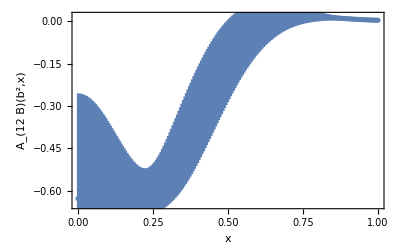

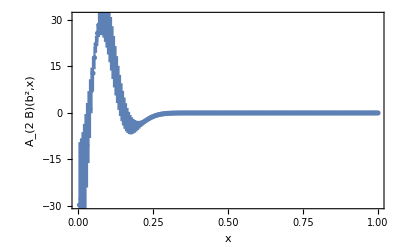

Sivers shift in GeV

-Graphics-

```mathematica
SiversShift[9,-2,7,3]
```

3 are SELECTED for fit!

7 are SELECTED for fit!

Fitting:    -> () = {⟨-0.17(12)⟩_(2902J), ⟨0.098(53)⟩_(2902J), ⟨0.061(30)⟩_(2902J)}, chisquareDoF = 0.585279
 Fitting:    -> () = {⟨1.57(34)⟩_(2902J), ⟨0.115(16)⟩_(2902J), ⟨0.095(19)⟩_(2902J)}, chisquareDoF = 0.766784
 Fitting:   -> () =                                                              -6
{⟨-0.0209(65)⟩_(2902J), ⟨-4.516(61) × 10  ⟩_(2902J), ⟨0.050(11)⟩_(2902J)} chisquareDoF = 0.45967
  = 9  = -3

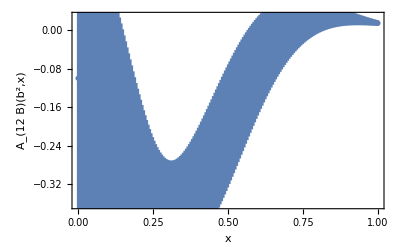

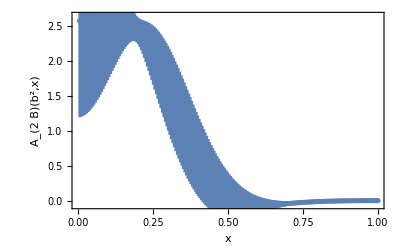

Sivers shift in GeV

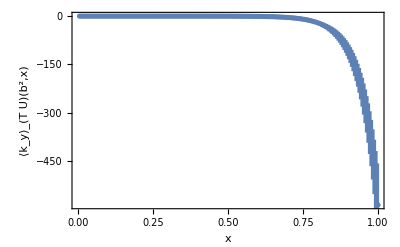

```mathematica
SiversShift[9,-3,7,3]
```

3 are SELECTED for fit!

7 are SELECTED for fit!

Fitting:    -> () = {⟨-0.17(12)⟩_(2902J), ⟨0.098(53)⟩_(2902J), ⟨0.061(30)⟩_(2902J)}, chisquareDoF = 0.585279
 Fitting:    -> () = {⟨1.57(34)⟩_(2902J), ⟨0.115(16)⟩_(2902J), ⟨0.095(19)⟩_(2902J)}, chisquareDoF = 0.766784
 Fitting:   -> () =                                                              -6
{⟨-0.0209(65)⟩_(2902J), ⟨-4.516(61) × 10  ⟩_(2902J), ⟨0.050(11)⟩_(2902J)} chisquareDoF = 0.45967
  = 9  = -3

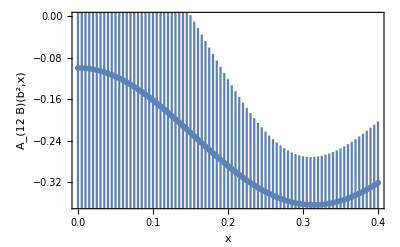

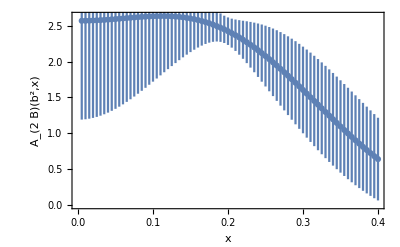

Sivers shift in GeV

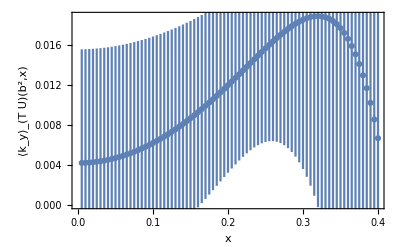

```mathematica
SiversShift[9,-3,7,3]
```

3 are SELECTED for fit!

7 are SELECTED for fit!

Fitting:    -> () = {⟨-0.006 ± 0.074⟩_(2902J), ⟨-0.007 ± 0.042⟩_(2902J), ⟨0.038(51)⟩_(2902J)}, chisquareDoF = 0.561808
 Fitting:    -> () = {⟨0.94(32)⟩_(2902J), ⟨0.120(32)⟩_(2902J), ⟨0.057(23)⟩_(2902J)}, chisquareDoF = 0.59455
 Fitting:   -> () = {⟨0.08 ± 0.14⟩_(2902J), ⟨-4.17(20)⟩_(2902J), ⟨0.35(11)⟩_(2902J)} chisquareDoF = 2.15555
  = 9  = -4

-Graphics-

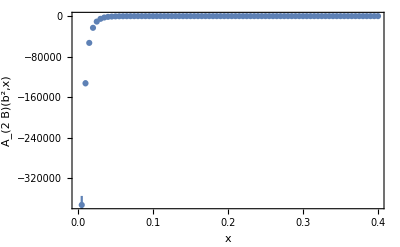

Sivers shift in GeV

-Graphics-

```mathematica
SiversShift[9,-4,7,3]
```

```mathematica
SiversShiftA2bRe[b2_,P1_,etaminForFit_, bminForFit_]:=Module[{dataforfitA12B, dataforfitA2B, dataforfitImA2B, fitJKA12B, fitParasA12B, chisqfitA12B, fitJKA2B, fitParasA2B, chisqfitA2B, fitJKImA2B, fitParasImA2B, chisqfitImA2B},
dataforfitA12B = Select[MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->A12B,PL->P1, bNum->even}],{etav, bL, bT,data}],#[[1]]>=etaminForFit&&Sqrt[#[[2]]^2+#[[3]]^2]>=bminForFit&];
dataforfitA2B = Select[MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->A2B,PL->P1, bNum->even}],{etav, bL, bT,data}],#[[1]]>=etaminForFit&&Sqrt[#[[2]]^2+#[[3]]^2]>=bminForFit&&#[[3]]==0&];
Print["",bminForFit," are SELECTED for fit!"];
Print["",etaminForFit," are SELECTED for fit!"];
modelfitA12B[x1_,x2_, x3_,{a_,c_, d_}]:=a*Exp[-0.5*x1]*Exp[-c*x2^2]*Exp[-d*x3^2];
modelfitA2B[x1_,x2_, x3_,{a_,c_, d_}]:=a*Exp[-0.5*x1]*Exp[-c*x2^2]*Exp[-d*x3^2];
fitJKA12B =JackknifeFit4D[dataforfitA12B,modelfitA12B[n, bL,bT,{a,c, d}],{{a, 2.5},{c,0.08}, {d,0.07}},{n,bL,bT}, modelfitA12B];
fitParasA12B=FitParameters/. fitJKA12B;
chisqfitA12B=chisquareDoF/. fitJKA12B;
fitJKA2B =JackknifeFit4D[dataforfitA2B,modelfitA2B[n, bL,bT,{a,c, d}],{{a, -8.15},{c,0.08}, {d,0.06}},{n,bL,bT}, modelfitA2B];
fitParasA2B=FitParameters/. fitJKA2B;
chisqfitA2B=chisquareDoF/. fitJKA2B;
Print["Fitting:    -> () = ",OutputForm[fitParasA12B], ", chisquareDoF = ", chisqfitA12B,"\n Fitting:    -> () = ",OutputForm[fitParasA2B], ", chisquareDoF = ", chisqfitA2B, "\n  = ",b2, "  = ",P1];
b2II = b2*fitParasA12B[[1]]/fitParasA12B[[1]];
II= fitParasA12B[[1]]/fitParasA12B[[1]];
fitaA12B =fitParasA12B[[1]];
fitbA12B=fitParasA12B[[2]];
fitcA12B =fitParasA12B[[3]];
fitaA2B =fitParasA2B[[1]];
fitbA2B=fitParasA2B[[2]];
fitcA2B =fitParasA2B[[3]];
MassN = MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->A12B,PL->P1}],MN][[1]];
A12BReprefactorPb=(fitbA12B-fitcA12B)/(P1*P1);
reducedratioA12B=fitaA12B/(Sqrt[2*A12BReprefactorPb]);
fourierA12B[x_, {reducedr_, A12BReprefactPb_, cA12B_}] :=Exp[-((x^2)/(4*A12BReprefactPb))]*Exp[-cA12B*b2]*reducedr;
A2BReprefactorPb=(fitbA2B-fitcA2B)/(P1*P1);
reducedratioA2B=fitaA2B/(Sqrt[2*A2BReprefactorPb]);
fourierA2B[x_, {reducedr_, A2BReprefactPb_, cA2B_}] :=Exp[-((x^2)/(4*A2BReprefactPb))]*Exp[-cA2B*b2]*reducedr;
massterm=-MassN*(197*0.0001/lata);
siversshiftxforplot={};
fourieA12Bxforplot={};
fourieA2Bxforplot={};
Do[
(*siversrforx = modelfitJackkifex[siversratio,{reducedratio1, fitbA12B, fitbA2B}, x];*)
fourierA12Bforx = modelfitJackkifex[fourierA12B,{reducedratioA12B, A12BReprefactorPb, fitcA12B}, x];
fourierREA2Bforx=modelfitJackkifex[fourierA2B,{reducedratioA2B, A2BReprefactorPb, fitcA2B}, x];
fourierA2Bforx=fourierREA2Bforx;
siversrforx=massterm*fourierA12Bforx/fourierA2Bforx;
AppendTo[siversshiftxforplot,{x,siversrforx}];
AppendTo[fourieA12Bxforplot,{x,fourierA12Bforx}];
AppendTo[fourieA2Bxforplot,{x,fourierA2Bforx}];
,{x,0,1, 0.005}];
MkErrA12B=MakeErrBars[fourieA12Bxforplot];
A12BPltrangMin=(MkErrA12B[[1]][[1]][[2]]+MkErrA12B[[1]][[2]][[1]][[1]])*0.5;
A12BPltrangMax=(MkErrA12B[[1]][[1]][[2]]+MkErrA12B[[1]][[2]][[1]][[2]])*1.2;
PlotfourieA12Bx = ErrorListPlot[MkErrA12B,FrameLabel->{ , }, Frame->True , PlotRange->Full];(* {{Automatic,Automatic},{0,0.0004}}*)
Print[PlotfourieA12Bx];
(*modelforxintgralA12B[b_]:=ArcTan[Sinh[π/(2 b)]];
xintegralA12B=modelJackk[modelforxintgralA12B, fitbA12B, fitaA12B* Sqrt[2/π]/(b2II+fitcA12B)];
Print[" ",OutputForm[xintegralA12B]];
Print["", OutputForm[MemDBGet[AmpDBPbbsq,MemDBSelect[AmpDBPbbsq,{A->A12B,PL->P1,etav->etavalue, bNum->even, bsquare->b2, Pb32by2Pi->0}],data][[1]]]];*)
MkErrA2B=MakeErrBars[fourieA2Bxforplot];
A2BPltrangMin=(MkErrA2B[[1]][[1]][[2]]+MkErrA2B[[1]][[2]][[1]][[1]])*0.5;
A2BPltrangMax=(MkErrA2B[[1]][[1]][[2]]+MkErrA2B[[1]][[2]][[1]][[2]])*2;
PlotfourieA2Bx= ErrorListPlot[MkErrA2B,FrameLabel->{ , }, Frame->True , PlotRange->Full];(*{{Automatic,Automatic},{0.0045,0.0055}}*)
Print[PlotfourieA2Bx];
(*modelforxintgralA2B[b_]:=ArcTan[Sinh[π/(2 b)]];
modelforxintgralA2BIM[b_]:=(2-2*Exp[-1/(4b)]);
xintegralA2B=modelJackk[modelforxintgralA2B, fitbA2B, fitaA2B* Sqrt[2/π]/(b2II+fitcA2B)]-modelJackk[modelforxintgralA2BIM, fitbImA2B, fitaImA2B/(22*Sqrt[2]*Sqrt[fitbImA2B]*(b2II+fitcImA2B))];
Print[" ",OutputForm[xintegralA2B]];
Print["", OutputForm[MemDBGet[AmpDBPbbsq,MemDBSelect[AmpDBPbbsq,{A->A2B,PL->P1,etav->etavalue, bNum->even, bsquare->b2, Pb32by2Pi->0}],data][[1]]]];*)
Print["Sivers shift in GeV"];
MkErrsiversshift=MakeErrBars[siversshiftxforplot];
SsPltrangMin=(MkErrsiversshift[[1]][[1]][[2]]-MkErrsiversshift[[1]][[2]][[1]][[1]])*0.5;
SsPltrangMax=(MkErrsiversshift[[1]][[1]][[2]]-MkErrsiversshift[[1]][[2]][[1]][[2]])*1.2;
Plotsivershift = ErrorListPlot[MkErrsiversshift,FrameLabel->{ , }, Frame->True , PlotRange->Full];(* PlotRange->{{Automatic,Automatic},{-0.3,0}}*)
Print[Plotsivershift]
(*Print[" ",OutputForm[massterm*xintegralA12B/xintegralA2B]];
Print["", OutputForm[(massterm*MemDBGet[AmpDBPbbsq,MemDBSelect[AmpDBPbbsq,{A->A12B,PL->P1,etav->etavalue, bNum->even, bsquare->b2, Pb32by2Pi->0}],data][[1]])/(MemDBGet[AmpDBPbbsq,MemDBSelect[AmpDBPbbsq,{A->A2B,PL->P1,etav->etavalue, bNum->even, bsquare->b2, Pb32by2Pi->0}],data][[1]])]];*)
(*Export["/Users/hariprashadravikumar/Downloads/Fourierx_A12B_"<>ToString[ampname]<>"_b_"<>ToString[bnum]<>"_P1_"<>ToString[P1]<>"_eta_"<>ToString[etavalue]<>".pdf",PlotfourieA12Bx,"PDF",ImageResolution->600];
Export["/Users/hariprashadravikumar/Downloads/Fourierx_A2B_"<>ToString[ampname]<>"_b_"<>ToString[bnum]<>"_P1_"<>ToString[P1]<>"_eta_"<>ToString[etavalue]<>".pdf",PlotfourieA2Bx,"PDF",ImageResolution->600];
Export["/Users/hariprashadravikumar/Downloads/Fourierx_SiversShift_"<>ToString[ampname]<>"_b_"<>ToString[bnum]<>"_P1_"<>ToString[P1]<>"_eta_"<>ToString[etavalue]<>".pdf",Plotsivershift,"PDF",ImageResolution->600];*)
];
```

2.75 are SELECTED for fit!

7 are SELECTED for fit!

Fitting:    -> () = {⟨-0.86(18)⟩_(2902J), ⟨0.094(18)⟩_(2902J), ⟨0.094(18)⟩_(2902J)}, chisquareDoF = 0.813952
 Fitting:    -> () = {⟨2.961(68)⟩_(2902J), ⟨0.0914(24)⟩_(2902J), ⟨0.0908(26)⟩_(2902J)}, chisquareDoF = 8.88789
  = 9  = -1

-Graphics-

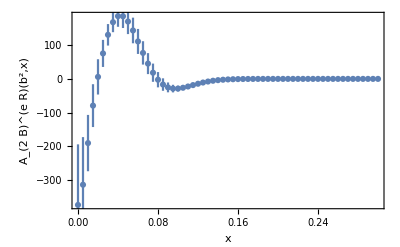

Sivers shift in GeV

-Graphics-

```mathematica
SiversShiftA2bRe[9,-1,7,2.75]
```

```mathematica
SiversShiftA2bRe[9,-1,7,2.5]
```

2.5 are SELECTED for fit!

7 are SELECTED for fit!

Fitting:    -> () = {⟨-0.86(18)⟩_(2902J), ⟨0.094(18)⟩_(2902J), ⟨0.094(18)⟩_(2902J)}, chisquareDoF = 0.813952
 Fitting:    -> () = {⟨2.961(68)⟩_(2902J), ⟨0.0914(24)⟩_(2902J), ⟨0.0908(26)⟩_(2902J)}, chisquareDoF = 8.88789
  = 9  = -1

-Graphics-

-Graphics-

Sivers shift in GeV

-Graphics-

3 are SELECTED for fit!

7 are SELECTED for fit!

Fitting:    -> () = {⟨-0.51(13)⟩_(2902J), ⟨0.080(19)⟩_(2902J), ⟨0.066(14)⟩_(2902J)}, chisquareDoF = 0.634404
 Fitting:    -> () = {⟨1.893(87)⟩_(2902J), ⟨0.0697(33)⟩_(2902J), ⟨0.0673(28)⟩_(2902J)}, chisquareDoF = 3.88468
  = 9  = -1

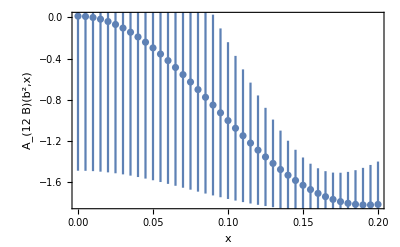

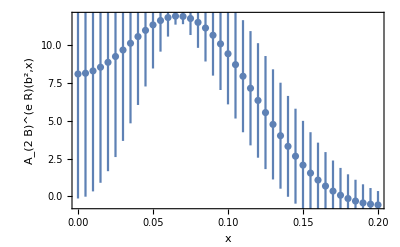

Sivers shift in GeV

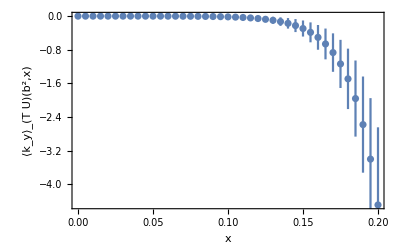

```mathematica
SiversShiftA2bRe[9,-1,7,3]
```

3 are SELECTED for fit!

6 are SELECTED for fit!

Fitting:    -> () = {⟨-0.469(78)⟩_(2902J), ⟨0.075(14)⟩_(2902J), ⟨0.0610(82)⟩_(2902J)}, chisquareDoF = 0.659288
 Fitting:    -> () = {⟨1.604(45)⟩_(2902J), ⟨0.0586(20)⟩_(2902J), ⟨0.0581(17)⟩_(2902J)}, chisquareDoF = 5.86841
  = 9  = -1

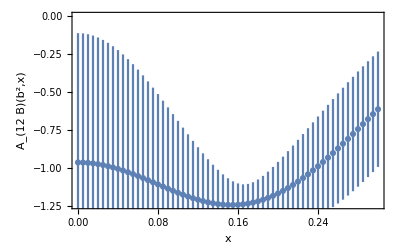

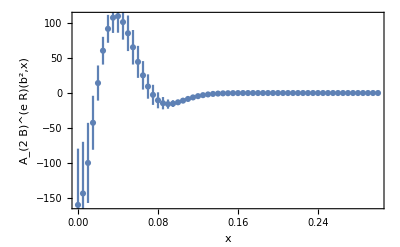

Sivers shift in GeV

-Graphics-

```mathematica
SiversShiftA2bRe[9,-1,6,3]
```

3 are SELECTED for fit!

7 are SELECTED for fit!

Fitting:    -> () = {⟨-0.36(11)⟩_(2902J), ⟨0.095(26)⟩_(2902J), ⟨0.066(15)⟩_(2902J)}, chisquareDoF = 0.931964
 Fitting:    -> () = {⟨1.87(19)⟩_(2902J), ⟨0.0912(67)⟩_(2902J), ⟨0.0889(78)⟩_(2902J)}, chisquareDoF = 1.37969
  = 9  = -2

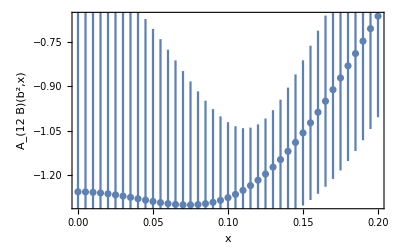

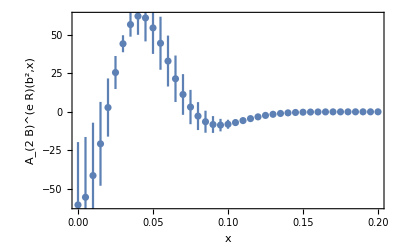

Sivers shift in GeV

-Graphics-

```mathematica
SiversShiftA2bRe[9,-2,7,3]
```

3 are SELECTED for fit!

7 are SELECTED for fit!

Fitting:    -> () = {⟨-0.36(11)⟩_(2902J), ⟨0.095(26)⟩_(2902J), ⟨0.066(15)⟩_(2902J)}, chisquareDoF = 0.931964
 Fitting:    -> () = {⟨1.87(19)⟩_(2902J), ⟨0.0912(67)⟩_(2902J), ⟨0.0889(78)⟩_(2902J)}, chisquareDoF = 1.37969
  = 9  = -2

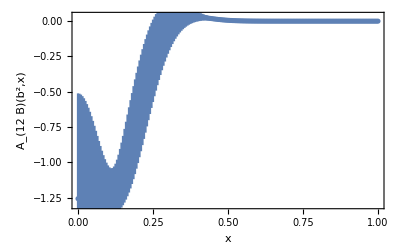

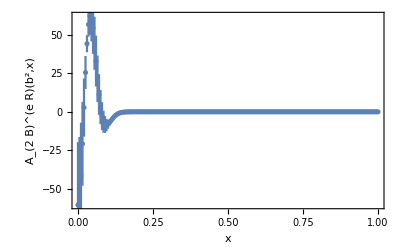

Sivers shift in GeV

-Graphics-

```mathematica
SiversShiftA2bRe[9,-2,7,3]
```

3 are SELECTED for fit!

7 are SELECTED for fit!

Fitting:    -> () = {⟨-0.17(12)⟩_(2902J), ⟨0.098(53)⟩_(2902J), ⟨0.061(30)⟩_(2902J)}, chisquareDoF = 0.585279
 Fitting:    -> () = {⟨1.57(34)⟩_(2902J), ⟨0.115(16)⟩_(2902J), ⟨0.095(19)⟩_(2902J)}, chisquareDoF = 0.766784
  = 9  = -3

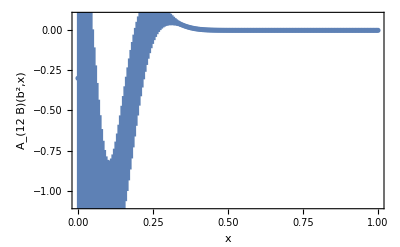

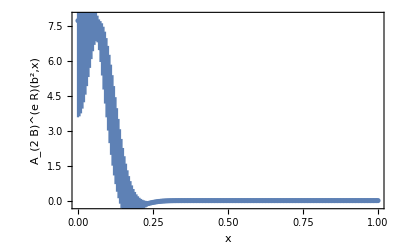

Sivers shift in GeV

-Graphics-

```mathematica
SiversShiftA2bRe[9,-3,7,3]
```

3 are SELECTED for fit!

7 are SELECTED for fit!

Fitting:    -> () = {⟨-0.006 ± 0.074⟩_(2902J), ⟨-0.007 ± 0.042⟩_(2902J), ⟨0.038(51)⟩_(2902J)}, chisquareDoF = 0.561808
 Fitting:    -> () = {⟨0.94(32)⟩_(2902J), ⟨0.120(32)⟩_(2902J), ⟨0.057(23)⟩_(2902J)}, chisquareDoF = 0.59455
  = 9  = -4

-Graphics-

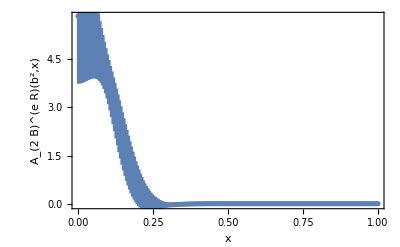

Sivers shift in GeV

-Graphics-

```mathematica
SiversShiftA2bRe[9,-4,7,3]
```

```mathematica
SiversShiftA2bRe[9,-2,7,3]
```

3 are SELECTED for fit!

7 are SELECTED for fit!

Fitting:    -> () = {⟨-0.36(11)⟩_(2902J), ⟨0.095(26)⟩_(2902J), ⟨0.066(15)⟩_(2902J)}, chisquareDoF = 0.931964
 Fitting:    -> () =                    3 - MantissaExponent[??][[2]]                                                                                                                                           3 - MantissaExponent[??][[2]]                                                                                                                                           3 - MantissaExponent[??][[2]]
{{⟨If[Sign[Round[10                              a]] == -1, -, ]<>        3 - MantissaExponent[??][[2]]    <>IntegerDigits[??]<>1<>2<>)⟩_(1J), {}}, {⟨If[Sign[Round[10                              c]] == -1, -, ]<>        3 - MantissaExponent[??][[2]]    <>IntegerDigits[??]<>1<>2<>)⟩_(1J), {}}, {⟨If[Sign[Round[10                              d]] == -1, -, ]<>        3 - MantissaExponent[??][[2]]    <>IntegerDigits[??]<>1<>2<>)⟩_(1J), {}}}
                                                                  Round[10                              a](                                                                                                                               Round[10                              c](                                                                                                                               Round[10                              d](, chisquareDoF = 0
  = 9  = -2

-Graphics-

-Graphics-

Sivers shift in GeV

-Graphics-

```mathematica
SiversShiftA2bReeta[b2_,P1_,etavalue_, bminForFit_]:=Module[{dataforfitA12B, dataforfitA2B, dataforfitImA2B, fitJKA12B, fitParasA12B, chisqfitA12B, fitJKA2B, fitParasA2B, chisqfitA2B, fitJKImA2B, fitParasImA2B, chisqfitImA2B},
dataforfitA12B = Select[MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->A12B,PL->P1, bNum->even, etav->etavalue}],{bL, bT,data}],Sqrt[#[[1]]^2+#[[2]]^2]>=bminForFit&];
dataforfitA2B = Select[MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->A2B,PL->P1, bNum->even, etav->etavalue}],{bL, bT,data}],Sqrt[#[[1]]^2+#[[2]]^2]>=bminForFit&];
Print["",bminForFit," are SELECTED for fit!"];
Print["",etaminForFit," are SELECTED for fit!"];
modelfitA12B[x2_, x3_,{a_,c_, d_}]:=a*Exp[-c*x2^2]*Exp[-d*x3^2];
modelfitA2B[x2_, x3_,{a_,c_, d_}]:=a*Exp[-c*x2^2]*Exp[-d*x3^2];
fitJKA12B =JackknifeFit3D[dataforfitA12B,modelfitA12B[bL,bT,{a,c, d}],{a,c,d},{bL,bT}, modelfitA12B];
fitParasA12B=FitParameters/. fitJKA12B;
chisqfitA12B=chisquareDoF/. fitJKA12B;
fitJKA2B =JackknifeFit3D[dataforfitA2B,modelfitA2B[bL,bT,{a,c, d}],{a,c,d},{bL,bT}, modelfitA2B];
fitParasA2B=FitParameters/. fitJKA2B;
chisqfitA2B=chisquareDoF/. fitJKA2B;
Print["Fitting:    -> () = ",OutputForm[fitParasA12B], ", chisquareDoF = ", chisqfitA12B,"\n Fitting:    -> () = ",OutputForm[fitParasA2B], ", chisquareDoF = ", chisqfitA2B, "\n  = ",b2, "  = ",P1];
b2II = b2*fitParasA12B[[1]]/fitParasA12B[[1]];
II= fitParasA12B[[1]]/fitParasA12B[[1]];
fitaA12B =fitParasA12B[[1]];
fitbA12B=fitParasA12B[[2]];
fitcA12B =fitParasA12B[[3]];
fitaA2B =fitParasA2B[[1]];
fitbA2B=fitParasA2B[[2]];
fitcA2B =fitParasA2B[[3]];
MassN = MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->A12B,PL->P1}],MN][[1]];
A12BReprefactorPb=(fitbA12B-fitcA12B)/(P1*P1);
reducedratioA12B=fitaA12B/(Sqrt[2*A12BReprefactorPb]);
fourierA12B[x_, {reducedr_, A12BReprefactPb_, cA12B_}] :=Exp[-((x^2)/(4*A12BReprefactPb))]*Exp[-cA12B*b2]*reducedr;
A2BReprefactorPb=(fitbA2B-fitcA2B)/(P1*P1);
reducedratioA2B=fitaA2B/(Sqrt[2*A2BReprefactorPb]);
fourierA2B[x_, {reducedr_, A2BReprefactPb_, cA2B_}] :=Exp[-((x^2)/(4*A2BReprefactPb))]*Exp[-cA2B*b2]*reducedr;
massterm=-MassN*(197*0.0001/lata);
siversshiftxforplot={};
fourieA12Bxforplot={};
fourieA2Bxforplot={};
Do[
(*siversrforx = modelfitJackkifex[siversratio,{reducedratio1, fitbA12B, fitbA2B}, x];*)
fourierA12Bforx = modelfitJackkifex[fourierA12B,{reducedratioA12B, A12BReprefactorPb, fitcA12B}, x];
fourierREA2Bforx=modelfitJackkifex[fourierA2B,{reducedratioA2B, A2BReprefactorPb, fitcA2B}, x];
fourierA2Bforx=fourierREA2Bforx;
siversrforx=massterm*fourierA12Bforx/fourierA2Bforx;
AppendTo[siversshiftxforplot,{x,siversrforx}];
AppendTo[fourieA12Bxforplot,{x,fourierA12Bforx}];
AppendTo[fourieA2Bxforplot,{x,fourierA2Bforx}];
,{x,0,1, 0.005}];
MkErrA12B=MakeErrBars[fourieA12Bxforplot];
A12BPltrangMin=(MkErrA12B[[1]][[1]][[2]]+MkErrA12B[[1]][[2]][[1]][[1]])*0.5;
A12BPltrangMax=(MkErrA12B[[1]][[1]][[2]]+MkErrA12B[[1]][[2]][[1]][[2]])*1.2;
PlotfourieA12Bx = ErrorListPlot[MkErrA12B,FrameLabel->{ , }, Frame->True , PlotRange->Full];(* {{Automatic,Automatic},{0,0.0004}}*)
Print[PlotfourieA12Bx];
(*modelforxintgralA12B[b_]:=ArcTan[Sinh[π/(2 b)]];
xintegralA12B=modelJackk[modelforxintgralA12B, fitbA12B, fitaA12B* Sqrt[2/π]/(b2II+fitcA12B)];
Print[" ",OutputForm[xintegralA12B]];
Print["", OutputForm[MemDBGet[AmpDBPbbsq,MemDBSelect[AmpDBPbbsq,{A->A12B,PL->P1,etav->etavalue, bNum->even, bsquare->b2, Pb32by2Pi->0}],data][[1]]]];*)
MkErrA2B=MakeErrBars[fourieA2Bxforplot];
A2BPltrangMin=(MkErrA2B[[1]][[1]][[2]]+MkErrA2B[[1]][[2]][[1]][[1]])*0.5;
A2BPltrangMax=(MkErrA2B[[1]][[1]][[2]]+MkErrA2B[[1]][[2]][[1]][[2]])*2;
PlotfourieA2Bx= ErrorListPlot[MkErrA2B,FrameLabel->{ , }, Frame->True , PlotRange->Full];(*{{Automatic,Automatic},{0.0045,0.0055}}*)
Print[PlotfourieA2Bx];
(*modelforxintgralA2B[b_]:=ArcTan[Sinh[π/(2 b)]];
modelforxintgralA2BIM[b_]:=(2-2*Exp[-1/(4b)]);
xintegralA2B=modelJackk[modelforxintgralA2B, fitbA2B, fitaA2B* Sqrt[2/π]/(b2II+fitcA2B)]-modelJackk[modelforxintgralA2BIM, fitbImA2B, fitaImA2B/(22*Sqrt[2]*Sqrt[fitbImA2B]*(b2II+fitcImA2B))];
Print[" ",OutputForm[xintegralA2B]];
Print["", OutputForm[MemDBGet[AmpDBPbbsq,MemDBSelect[AmpDBPbbsq,{A->A2B,PL->P1,etav->etavalue, bNum->even, bsquare->b2, Pb32by2Pi->0}],data][[1]]]];*)
Print["Sivers shift in GeV"];
MkErrsiversshift=MakeErrBars[siversshiftxforplot];
SsPltrangMin=(MkErrsiversshift[[1]][[1]][[2]]-MkErrsiversshift[[1]][[2]][[1]][[1]])*0.5;
SsPltrangMax=(MkErrsiversshift[[1]][[1]][[2]]-MkErrsiversshift[[1]][[2]][[1]][[2]])*1.2;
Plotsivershift = ErrorListPlot[MkErrsiversshift,FrameLabel->{ , }, Frame->True , PlotRange->Full];(* PlotRange->{{Automatic,Automatic},{-0.3,0}}*)
Print[Plotsivershift]
(*Print[" ",OutputForm[massterm*xintegralA12B/xintegralA2B]];
Print["", OutputForm[(massterm*MemDBGet[AmpDBPbbsq,MemDBSelect[AmpDBPbbsq,{A->A12B,PL->P1,etav->etavalue, bNum->even, bsquare->b2, Pb32by2Pi->0}],data][[1]])/(MemDBGet[AmpDBPbbsq,MemDBSelect[AmpDBPbbsq,{A->A2B,PL->P1,etav->etavalue, bNum->even, bsquare->b2, Pb32by2Pi->0}],data][[1]])]];*)
(*Export["/Users/hariprashadravikumar/Downloads/Fourierx_A12B_"<>ToString[ampname]<>"_b_"<>ToString[bnum]<>"_P1_"<>ToString[P1]<>"_eta_"<>ToString[etavalue]<>".pdf",PlotfourieA12Bx,"PDF",ImageResolution->600];
Export["/Users/hariprashadravikumar/Downloads/Fourierx_A2B_"<>ToString[ampname]<>"_b_"<>ToString[bnum]<>"_P1_"<>ToString[P1]<>"_eta_"<>ToString[etavalue]<>".pdf",PlotfourieA2Bx,"PDF",ImageResolution->600];
Export["/Users/hariprashadravikumar/Downloads/Fourierx_SiversShift_"<>ToString[ampname]<>"_b_"<>ToString[bnum]<>"_P1_"<>ToString[P1]<>"_eta_"<>ToString[etavalue]<>".pdf",Plotsivershift,"PDF",ImageResolution->600];*)
];
```

3 are SELECTED for fit!

etaminForFit are SELECTED for fit!

Fitting:    -> () =                                                          3
{⟨595.0(42)⟩_(2902J), ⟨14.7(26) × 10 ⟩_(2902J), ⟨77.29(47)⟩_(2902J)}, chisquareDoF = 13.3434
 Fitting:    -> () = {⟨0.0510(17)⟩_(2902J), ⟨0.0613(24)⟩_(2902J), ⟨0.0603(20)⟩_(2902J)}, chisquareDoF = 5.10225
  = 9  = -1

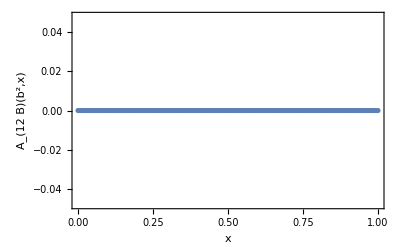

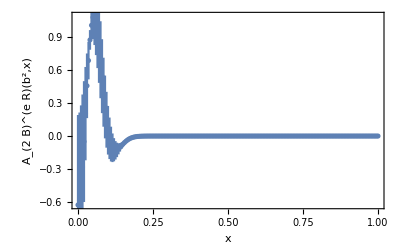

Sivers shift in GeV

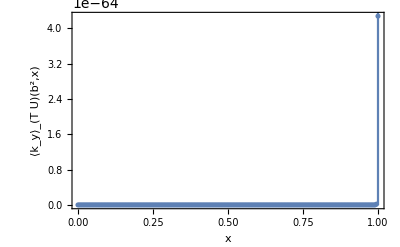

```mathematica
SiversShiftA2bReeta[9,-1,7,3]
```

```mathematica
SiversShiftA2bReeta[9,-2,7,3]
```

3 are SELECTED for fit!

etaminForFit are SELECTED for fit!

Fitting:    -> () =                                                          3
{⟨611.4(33)⟩_(2902J), ⟨10.5(23) × 10 ⟩_(2902J), ⟨75.47(37)⟩_(2902J)}, chisquareDoF = 9.74438
 Fitting:    -> () = {⟨0.0504(39)⟩_(2902J), ⟨0.0815(52)⟩_(2902J), ⟨0.0808(58)⟩_(2902J)}, chisquareDoF = 1.55872
  = 9  = -2

-Graphics-

-Graphics-

Sivers shift in GeV

-Graphics-

3 are SELECTED for fit!

etaminForFit are SELECTED for fit!

Fitting:    -> () =                                                         3
{⟨628.0(45)⟩_(2902J), ⟨5.7(31) × 10 ⟩_(2902J), ⟨73.62(50)⟩_(2902J)}, chisquareDoF = 2.27403
 Fitting:    -> () = {⟨0.0419(72)⟩_(2902J), ⟨0.101(12)⟩_(2902J), ⟨0.086(15)⟩_(2902J)}, chisquareDoF = 0.876719
  = 9  = -3

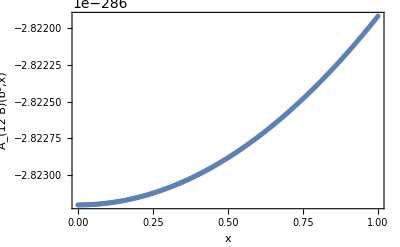

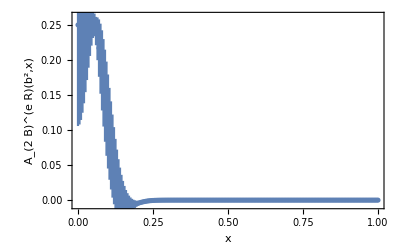

Sivers shift in GeV

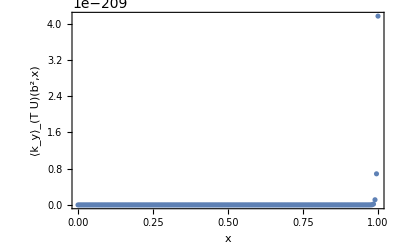

```mathematica
SiversShiftA2bReeta[9,-3,7,3]
```

3 are SELECTED for fit!

etaminForFit are SELECTED for fit!

Fitting:    -> () =                                                        3
{⟨615(11)⟩_(2902J), ⟨22.0(75) × 10 ⟩_(2902J), ⟨75.0(12)⟩_(2902J)}, chisquareDoF = 1.93348
 Fitting:    -> () = {⟨0.4976(28)⟩_(2902J), ⟨0.02864(18)⟩_(2902J), ⟨0.02722(15)⟩_(2902J)}, chisquareDoF = 14.6305
  = 9  = -1

-Graphics-

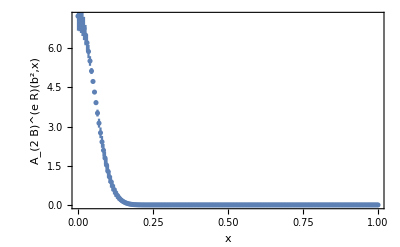

Sivers shift in GeV

$Aborted

```mathematica
SiversShiftA2bReeta[9,-1,0,3]
```

0 are SELECTED for fit!

etaminForFit are SELECTED for fit!

Fitting:    -> () = {⟨-0.0092(33)⟩_(2902J), ⟨0.0205(74)⟩_(2902J), ⟨0.0343(73)⟩_(2902J)}, chisquareDoF = 0.494745
 Fitting:    -> () = {⟨0.5546(30)⟩_(2902J), ⟨0.03197(18)⟩_(2902J), ⟨0.03073(16)⟩_(2902J)}, chisquareDoF = 39.1827
  = 9  = -1

-Graphics-

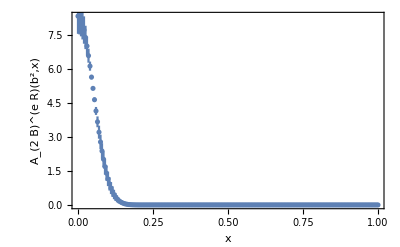

Sivers shift in GeV

-Graphics-

```mathematica
SiversShiftA2bReeta[9,-1,0,0]
```

0 are SELECTED for fit!

etaminForFit are SELECTED for fit!

Fitting:    -> () =                                                                                                   3
{⟨564(34)⟩_(2902J), ⟨42.45(75)⟩_(2902J), ⟨-6.40(11) × 10 ⟩_(2902J)}, chisquareDoF = 4545.57
 Fitting:    -> () = {⟨0.5608(48)⟩_(2902J), ⟨0.03858(37)⟩_(2902J), ⟨0.03094(26)⟩_(2902J)}, chisquareDoF = 11.6977
  = 9  = -2

-Graphics-

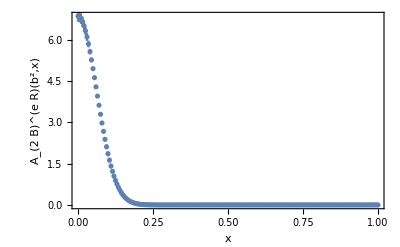

Sivers shift in GeV

-Graphics-

```mathematica
SiversShiftA2bReeta[9,-2,0,0]
```

0 are SELECTED for fit!

etaminForFit are SELECTED for fit!

Fitting:    -> () =                                                          3
{⟨66.3(76)⟩_(2902J), ⟨-33.2(15) × 10 ⟩_(2902J), ⟨0.8 ± 71.⟩_(2902J)}, chisquareDoF = 270.805
 Fitting:    -> () = {⟨0.5638(95)⟩_(2902J), ⟨0.0501(11)⟩_(2902J), ⟨0.03120(52)⟩_(2902J)}, chisquareDoF = 2.22164
  = 9  = -3

-Graphics-

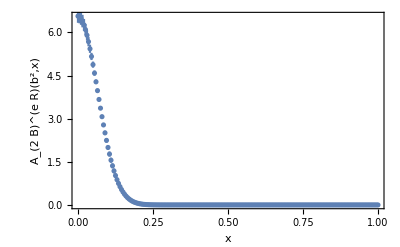

Sivers shift in GeV

-Graphics-

```mathematica
SiversShiftA2bReeta[9,-3,0,0]
```

0 are SELECTED for fit!

etaminForFit are SELECTED for fit!

Fitting:    -> () = {⟨0.0088(74)⟩_(2902J), ⟨0.031(25)⟩_(2902J), ⟨0.016(11)⟩_(2902J)}, chisquareDoF = 0.0970696
 Fitting:    -> () = {⟨0.591(22)⟩_(2902J), ⟨0.0654(33)⟩_(2902J), ⟨0.0309(11)⟩_(2902J)}, chisquareDoF = 0.529712
  = 9  = -4

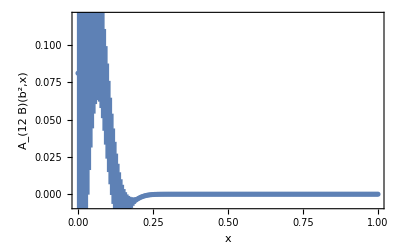

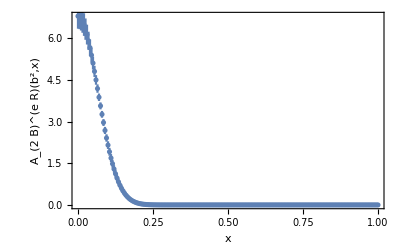

Sivers shift in GeV

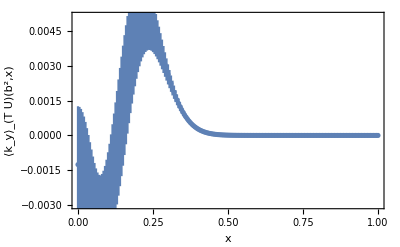

```mathematica
SiversShiftA2bReeta[9,-4,0,0]
```

```mathematica
FourierA2bReeta[b2_,P1_,etavalue_, bminForFit_]:=Module[{dataforfitA12B, dataforfitA2B, dataforfitImA2B, fitJKA12B, fitParasA12B, chisqfitA12B, fitJKA2B, fitParasA2B, chisqfitA2B, fitJKImA2B, fitParasImA2B, chisqfitImA2B,fourierA2Bforx,fourierREA2Bforx},
dataforfitA2B = Select[MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->A2B,PL->P1, bNum->even, etav->etavalue}],{bL, bT,data}],Sqrt[#[[1]]^2+#[[2]]^2]>=bminForFit&];
Print["",bminForFit," are SELECTED for fit!"];
modelfitA2B[x2_, x3_,{a_,c_, d_}]:=a*Exp[-c*x2^2]*Exp[-d*x3^2];
fitJKA2B =JackknifeFit3D[dataforfitA2B,modelfitA2B[bL,bT,{a,c, d}],{a,c,d},{bL,bT}, modelfitA2B];
fitParasA2B=FitParameters/. fitJKA2B;
chisqfitA2B=chisquareDoF/. fitJKA2B;
Print["Fitting:    -> () = ",OutputForm[fitParasA2B], ", chisquareDoF = ", chisqfitA2B, "\n  = ",b2, "  = ",P1];
b2II = b2*fitParasA12B[[1]]/fitParasA12B[[1]];
II= fitParasA12B[[1]]/fitParasA12B[[1]];
fitaA2B =fitParasA2B[[1]];
fitbA2B=fitParasA2B[[2]];
fitcA2B =fitParasA2B[[3]];
A2BReprefactorPb=(fitbA2B-fitcA2B);
reducedratioA2B=fitaA2B/(Sqrt[2*A2BReprefactorPb]);
fourierA2B[x_, {reducedr_, A2BReprefactPb_, cA2B_}] :=Exp[-((x^2)/(4*A2BReprefactPb))]*Exp[-cA2B*b2]*reducedr;
fourieA2Bxforplot={};
Do[
fourierREA2Bforx=modelfitJackkifex[fourierA2B,{reducedratioA2B, A2BReprefactorPb, fitcA2B}, x];
fourierA2Bforx=fourierREA2Bforx;
AppendTo[fourieA2Bxforplot,{x,fourierA2Bforx}];
,{x,0,1, 0.005}];
MkErrA2B=MakeErrBars[fourieA2Bxforplot];
PlotfourieA2Bx= ErrorListPlot[MkErrA2B,FrameLabel->{ , }, Frame->True , PlotRange->Full];(*{{Automatic,Automatic},{0.0045,0.0055}}*)
Print[PlotfourieA2Bx];
];
```

3 are SELECTED for fit!

Fitting:    -> () = {⟨0.0391(45)⟩_(2902J), ⟨0.0986(79)⟩_(2902J), ⟨0.0965(95)⟩_(2902J)}, chisquareDoF = 1.35456
  = 9  = -2

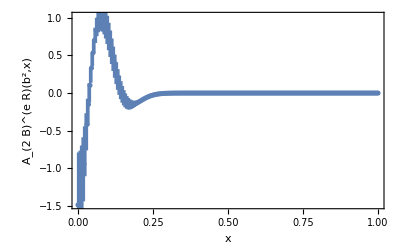

```mathematica
FourierA2bReeta[9,-2,8,3]
```

3 are SELECTED for fit!

Fitting:    -> () = {⟨0.0379(22)⟩_(2902J), ⟨0.0759(41)⟩_(2902J), ⟨0.0735(38)⟩_(2902J)}, chisquareDoF = 2.99266
  = 9  = -1

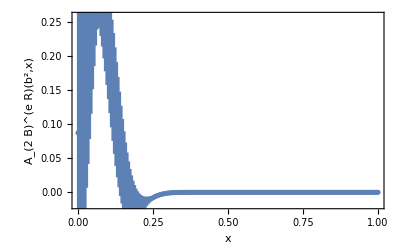

```mathematica
FourierA2bReeta[9,-1,8,3]
```

3 are SELECTED for fit!

Fitting:    -> () = {⟨0.0290(84)⟩_(2902J), ⟨0.119(21)⟩_(2902J), ⟨0.098(25)⟩_(2902J)}, chisquareDoF = 0.759837
  = 9  = -3

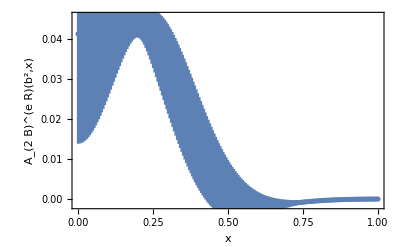

```mathematica
FourierA2bReeta[9,-3,8,3]
```

3 are SELECTED for fit!

Fitting:    -> () = {⟨0.0163(69)⟩_(2902J), ⟨0.126(39)⟩_(2902J), ⟨0.050(27)⟩_(2902J)}, chisquareDoF = 0.507327
  = 9  = -4

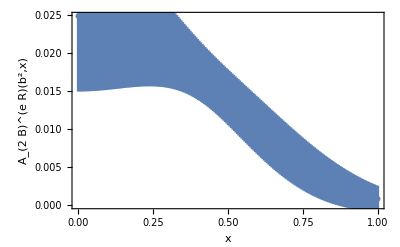

```mathematica
FourierA2bReeta[9,-4,8,3]
```